# Derivation of Chen Rules

This notebook contains derivation of Chen Rules for PP-STM code

```mathematica
(* Ns=1/Sqrt[4Pi]; Np=Sqrt[3]*Ns; Nd=Sqrt[15]*Ns; Nd2=Sqrt[5] *0.5)
```

```mathematica
(*decay=-1;*)
revrr[x_,y_,z_]:=1/Sqrt[x*x+y*y+z*z];
R[x_,y_,z_,decay_]:=Exp[-decay*Sqrt[x*x+y*y+z*z]];
Y0[x_,y_,z_]:=Ns;
Yx[x_,y_,z_]:=Np*x*revrr[x,y,z];
Yy[x_,y_,z_]:=Np*y*revrr[x,y,z];
Yz[x_,y_,z_]:=Np*z*revrr[x,y,z];
Yxy[x_,y_,z_]:=Nd*x*y*revrr[x,y,z]^2;
Yxz[x_,y_,z_]:=Nd*x*z*revrr[x,y,z]^2;
Yz2[x_,y_,z_]:=Nd2*(3*z*z*revrr[x,y,z]^2-1);(*0.5*(3*dR.z*dR.z*rev_rr*rev_rr-1)*)
Yyz[x_,y_,z_]:=Nd*y*z*revrr[x,y,z]^2;
Yx2y2[x_,y_,z_]:=0.5*Nd*(x*x-y*y)*revrr[x,y,z]^2;
S[x_,y_,z_,decay_]:=R[x,y,z,decay]*Y0[x,y,z];
Px[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yx[x,y,z];
Py[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yy[x,y,z];
Pz[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yz[x,y,z];
Dxy[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yxy[x,y,z];
Dxz[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yxz[x,y,z];
Dz2[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yz2[x,y,z];
Dyz[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yyz[x,y,z];
Dx2y2[x_,y_,z_,decay_]:=R[x,y,z,decay]*Yx2y2[x,y,z];
```

```mathematica
Print["s-tip:"]
{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay],
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]}//TableForm

Print["p_x-tip:"]
D[-1*{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay],
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]},x]//TableForm

Print["p_y-tip:"]
D[-1*{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay],
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]},y]//TableForm

Print["p_z-tip:"]
D[-1*{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay],
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]},z]//TableForm
```

s-tip:

ⅇ^(-decay √(x^2+y^2+z^2)) Ns
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y)/(x^2+y^2+z^2)
(ⅇ^(-decay √(x^2+y^2+z^2)) Nd x z)/(x^2+y^2+z^2)
ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 (-1+(3 z^2)/(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Nd y z)/(x^2+y^2+z^2)
(0.5 ⅇ^(-decay √(x^2+y^2+z^2)) Nd (x^2-y^2))/(x^2+y^2+z^2)

p_x-tip:

(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns x)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x^2)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x^2)/(x^2+y^2+z^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x y)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x y)/(x^2+y^2+z^2)
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x z)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x z)/(x^2+y^2+z^2)
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x^2 y)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x^2 y)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd y)/(x^2+y^2+z^2)
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x^2 z)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x^2 z)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd z)/(x^2+y^2+z^2)
(6 ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 x z^2)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 x (-1+(3 z^2)/(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^(3/2))
(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd x (x^2-y^2))/((x^2+y^2+z^2)^2)+(0.5 decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x (x^2-y^2))/((x^2+y^2+z^2)^(3/2))-(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd x)/(x^2+y^2+z^2)

p_y-tip:

(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns y)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x y)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x y)/(x^2+y^2+z^2)
(ⅇ^(-decay √(x^2+y^2+z^2)) Np y^2)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y^2)/(x^2+y^2+z^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np y z)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y z)/(x^2+y^2+z^2)
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y^2)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y^2)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd x)/(x^2+y^2+z^2)
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^(3/2))
(6 ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 y z^2)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 y (-1+(3 z^2)/(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd y^2 z)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd y^2 z)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd z)/(x^2+y^2+z^2)
(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd y (x^2-y^2))/((x^2+y^2+z^2)^2)+(0.5 decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd y (x^2-y^2))/((x^2+y^2+z^2)^(3/2))+(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd y)/(x^2+y^2+z^2)

p_z-tip:

(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns z)/(√(x^2+y^2+z^2))
(ⅇ^(-decay √(x^2+y^2+z^2)) Np x z)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x z)/(x^2+y^2+z^2)
(ⅇ^(-decay √(x^2+y^2+z^2)) Np y z)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y z)/(x^2+y^2+z^2)
(ⅇ^(-decay √(x^2+y^2+z^2)) Np z^2)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np z^2)/(x^2+y^2+z^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np)/(√(x^2+y^2+z^2))
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x y z)/((x^2+y^2+z^2)^(3/2))
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd x z^2)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x z^2)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd x)/(x^2+y^2+z^2)
-ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 (-(6 z^3)/((x^2+y^2+z^2)^2)+(6 z)/(x^2+y^2+z^2))+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd2 z (-1+(3 z^2)/(x^2+y^2+z^2)))/(√(x^2+y^2+z^2))
(2 ⅇ^(-decay √(x^2+y^2+z^2)) Nd y z^2)/((x^2+y^2+z^2)^2)+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd y z^2)/((x^2+y^2+z^2)^(3/2))-(ⅇ^(-decay √(x^2+y^2+z^2)) Nd y)/(x^2+y^2+z^2)
(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd (x^2-y^2) z)/((x^2+y^2+z^2)^2)+(0.5 decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd (x^2-y^2) z)/((x^2+y^2+z^2)^(3/2))

```mathematica
(* D-tip orbitals - only for SP basis on the sample *)
Print["d_xz-tip:"]
D[D[{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay](*,
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]*)},x],z]//TableForm

Print["d_yz-tip:"]
D[D[{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay](*,
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]*)},y],z]//TableForm

Print["d_z2-tip:"] (* Beware - standars dz2 orbital in DFT is dz2-1/3r2 ; therefore this is not perfect dz2 orb. *)
D[D[{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay](*,
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]*)},z],z]-1/3*decay^2{S[x,y,z,decay],
Px[x,y,z,decay],
Py[x,y,z,decay],
Pz[x,y,z,decay](*,
Dxy[x,y,z,decay],
Dxz[x,y,z,decay],
Dz2[x,y,z,decay],
Dyz[x,y,z,decay],
Dx2y2[x,y,z,decay]*)}//TableForm
```

d_xz-tip:

(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns x z)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Ns x z)/(x^2+y^2+z^2)
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np x^2 z)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x^2 z)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x^2 z)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/(x^2+y^2+z^2)
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^2)+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^(3/2))
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/(x^2+y^2+z^2)

d_yz-tip:

(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns y z)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Ns y z)/(x^2+y^2+z^2)
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^2)+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x y z)/((x^2+y^2+z^2)^(3/2))
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np y^2 z)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y^2 z)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np y^2 z)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/(x^2+y^2+z^2)
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/(x^2+y^2+z^2)

d_z2-tip:

-1/3 decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Ns+(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns z^2)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Ns z^2)/(x^2+y^2+z^2)-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Ns)/(√(x^2+y^2+z^2))
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x z^2)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/(x^2+y^2+z^2)-(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np x)/(3 √(x^2+y^2+z^2))
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^2)-(ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np y z^2)/((x^2+y^2+z^2)^(3/2))-(decay ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/(x^2+y^2+z^2)-(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np y)/(3 √(x^2+y^2+z^2))
(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np z^3)/((x^2+y^2+z^2)^(5/2))+(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np z^3)/((x^2+y^2+z^2)^2)-(3 ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/((x^2+y^2+z^2)^(3/2))+(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np z^3)/((x^2+y^2+z^2)^(3/2))-(3 decay ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/(x^2+y^2+z^2)-(decay^2 ⅇ^(-decay √(x^2+y^2+z^2)) Np z)/(3 √(x^2+y^2+z^2))

Some older tests:

```mathematica
FullSimplify[(decay ⅇ^(decay √(x^2+y^2+z^2)) Ns x)/(√(x^2+y^2+z^2))-decay*S[x,y,z,decay]*x*revrr[x,y,z]]
```

0

```mathematica
Expand[Px[x,y,z,decay]]
```

(ⅇ^(decay √(x^2+y^2+z^2)) Np x)/(√(x^2+y^2+z^2))

```mathematica
FullSimplify[(-(ⅇ^(decay √(x^2+y^2+z^2)) Np x^2)/((x^2+y^2+z^2)^(3/2))+(decay ⅇ^(decay √(x^2+y^2+z^2)) Np x^2)/(x^2+y^2+z^2)+(ⅇ^(decay √(x^2+y^2+z^2)) Np)/(√(x^2+y^2+z^2)))-(-1*Px[x,y,z,decay]*x*revrr[x,y,z]^2+decay*Px[x,y,z,decay]*x*revrr[x,y,z]+Px[x,y,z,decay]/x)]
```

0

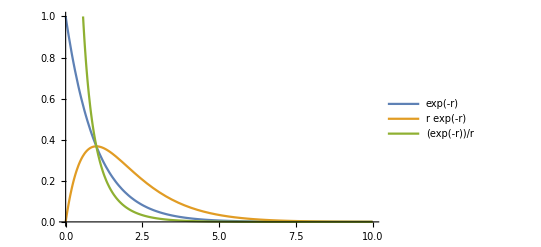

```mathematica
Plot[{Exp[-r],r*Exp[-r],Exp[-r]/r},{r,0,10},PlotRange->{0,1},PlotLegends->"Expressions"]
```

```mathematica
Integrate[r^2*(Exp[-ζ*r])^2,{r,0,Infinity}]
```

ConditionalExpression[1/(4 ζ^3),Re[ζ]>0]

```mathematica
Integrate[r^2*((2ζ^(3/2))Exp[-ζ*r])^2,{r,0,Infinity}]
```

ConditionalExpression[1,Re[ζ]>0]

```mathematica
f[x,y,z]:=Exp[-Norm]
```

```mathematica
NumberForm[Pi*4//N,8]
```

12.566371

```mathematica
(*PLOTING PART *)
```

```mathematica
aB=1/1.889725989;
path="~/Documents/WORK/probe_particle_code/ProbeSTM/test_single_atom/";
fireInter=Import[path<>"interaction_C_C.dat" ,"Table",HeaderLines->3];
numInter=fireInter[[1,1]]
headerInter=fireInter[[Range[2,numInter+1],{1,2,3}]]//TableForm
fireInter=Drop[fireInter,numInter+1];
fireInter[[All,1]]=fireInter[[All,1]]*aB;
sspInter=Import[path<>"s_sp_lines.dat" ,"Table",HeaderLines->0];
pxspInter=Import[path<>"px_sp_lines.dat" ,"Table",HeaderLines->0];
pyspInter=Import[path<>"py_sp_lines.dat" ,"Table",HeaderLines->0];
pzspInter=Import[path<>"pz_sp_lines.dat" ,"Table",HeaderLines->0];
```

19

0 | 0 | 0
0 | 1 | 0
0 | 2 | 0
1 | 0 | 0
1 | 1 | -1
1 | 1 | 0
1 | 1 | 1
1 | 2 | -1
1 | 2 | 0
1 | 2 | 1
2 | 0 | 0
2 | 1 | -1
2 | 1 | 0
2 | 1 | 1
2 | 2 | -2
2 | 2 | -1
2 | 2 | 0
2 | 2 | 1
2 | 2 | 2

```mathematica
(* Follows plotted C - C hoppings calculated by Fireball for Cesar's code. I think it's my hoppings 
2nd plot are currents for two atoms depending on distance from PP-STM code; probably nowadays results would be a little bit different (just quantitatively, not qualitatively) since there were few mistakes in the former versions of PP-STM *)
```

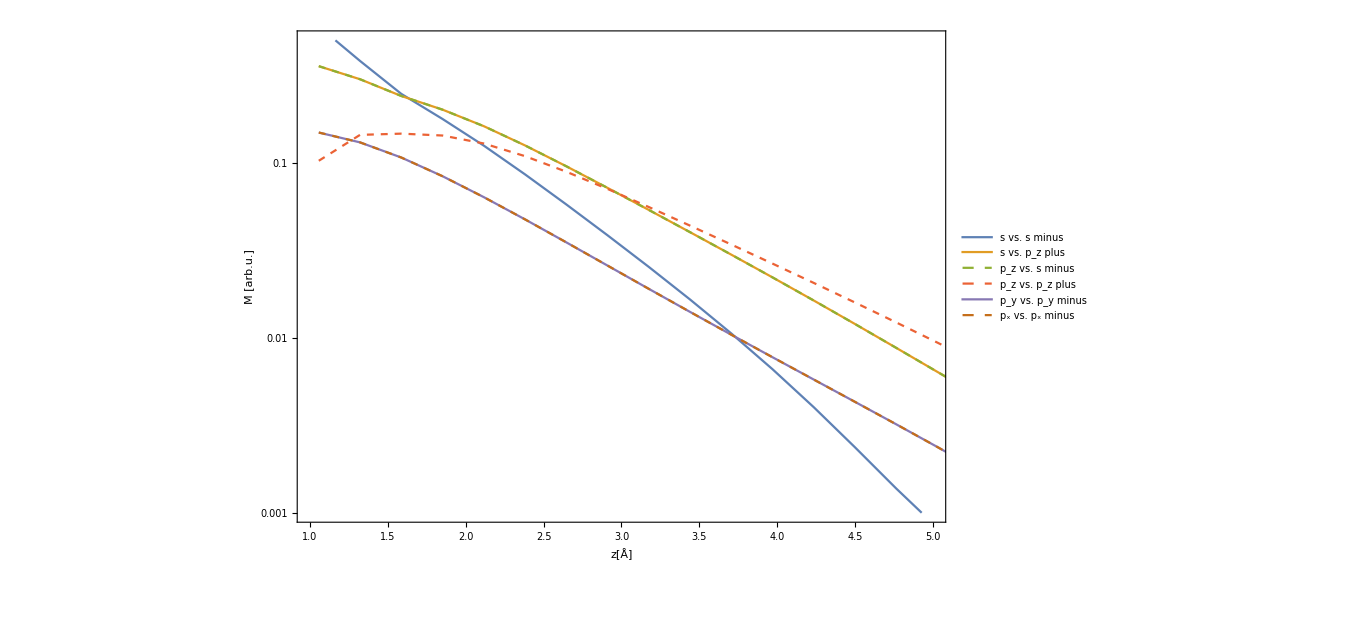

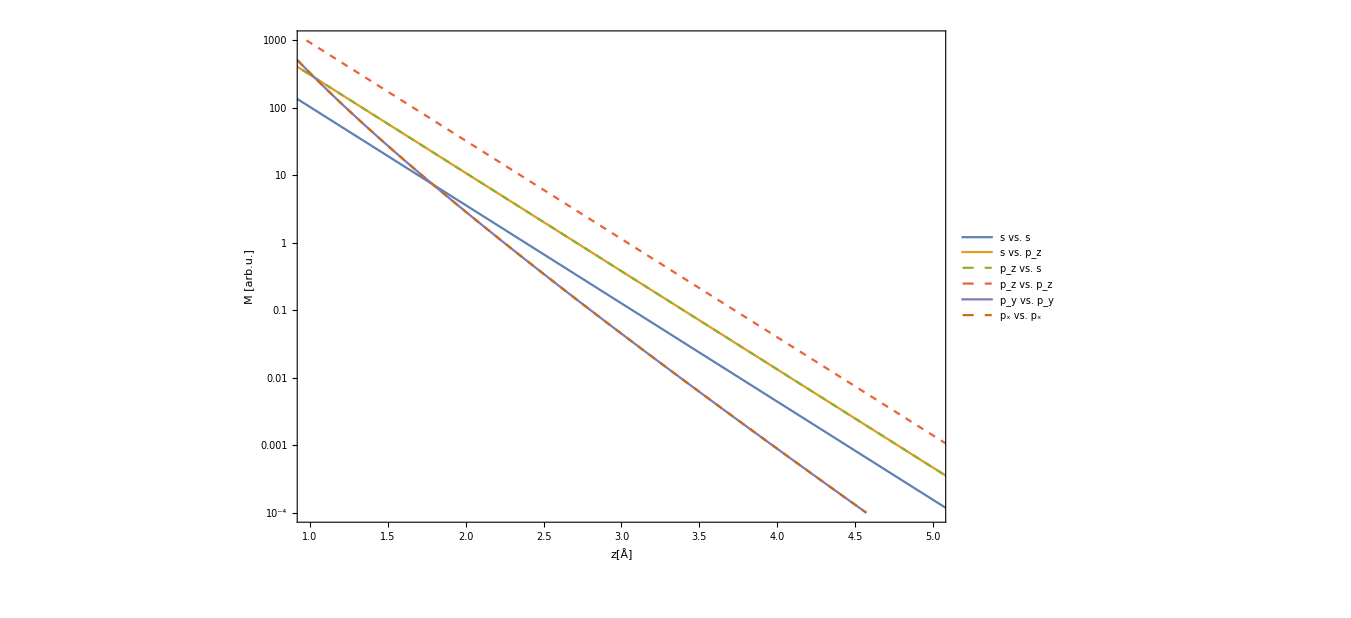

```mathematica
ListLogPlot[Abs[{fireInter[[All,{1,2}]],fireInter[[All,{1,3}]],fireInter[[All,{1,5}]],fireInter[[All,{1,7}]],fireInter[[All,{1,6}]],fireInter[[All,{1,8}]]}],Joined->True,PlotStyle->{Automatic,Automatic,Dashed,Dashed,Automatic,Dashed},Axes->False,Frame->{True,True,False,False},FrameLabel->{"z[Å]","M [arb.u.]"},PlotLegends->LineLegend[{"s vs. s minus","s vs. p_z plus","p_z vs. s minus","p_z vs. p_z plus","p_y vs. p_y minus","p_x vs. p_x minus"}],ImageSize->1000,PlotRange->{{1,5},{10^-3,0.5}}]
ListLogPlot[Abs[{sspInter[[All,{1,2}]],sspInter[[All,{1,3}]],pzspInter[[All,{1,2}]],pzspInter[[All,{1,3}]],pxspInter[[All,{1,4}]],pyspInter[[All,{1,5}]]}],Joined->True,Axes->False,Frame->{True,True,False,False},FrameLabel->{"z[Å]","M [arb.u.]"},PlotStyle->{Automatic,Automatic,Dashed,Dashed,Automatic,Dashed},PlotLegends->LineLegend[{"s vs. s","s vs. p_z","p_z vs. s","p_z vs. p_z","p_y vs. p_y","p_x vs. p_x"}],ImageSize->1000,PlotRange->{{1,5},{10^-4,10^3}}]
```

```mathematica
fireInter[[All,{1,8}]]
```

{{1.05835,-0.166601},{1.32294,-0.165249},{1.58753,-0.131312},{1.85212,-0.0910992},{2.11671,-0.0589395},{2.3813,-0.0374393},{2.64589,-0.024031},{2.91047,-0.01574},{3.17506,-0.010512},{3.43965,-0.00712418},{3.70424,-0.00487543},{3.96883,-0.00335644},{4.23342,-0.00231862},{4.49801,-0.00160526},{4.7626,-0.00111253},{5.02718,-0.000771854},{5.29177,-0.000535694},{5.55636,-0.000371844},{5.82095,-0.00025817},{6.08554,-0.000179022},{6.35013,-0.000124108},{6.61472,-0.000085914},{6.8793,-0.0000593689},{7.14389,-0.0000408954},{7.40848,-0.0000281369},{7.67307,-0.000019328},{7.93766,-0.0000132772},{8.20225,-9.17011×10^-6},{8.46684,-6.35379×10^-6},{8.73142,-4.42073×10^-6},{8.99601,-3.08728×10^-6},{9.2606,-2.1643×10^-6},{9.52519,-1.52321×10^-6},{9.78978,-1.07614×10^-6},{10.0544,-7.62865×10^-7},{10.319,-5.42045×10^-7},{10.5835,-3.85503×10^-7},{10.8481,-2.73503×10^-7},{11.1127,-1.92584×10^-7},{11.3773,-1.33328×10^-7},{11.6419,-8.92247×10^-8},{11.9065,-5.53637×10^-8},{12.1711,-2.81481×10^-8},{12.4357,-4.66312×10^-9},{12.7003,1.75767×10^-8},{12.9648,4.08661×10^-8},{13.2294,6.75075×10^-8},{13.494,9.9998×10^-8},{13.7586,1.41213×10^-7},{14.0232,1.94587×10^-7},{14.2878,2.6429×10^-7},{14.5524,3.55372×10^-7},{14.817,4.73839×10^-7},{15.0816,6.26544×10^-7},{15.3461,8.20765×10^-7},{15.6107,1.06291×10^-6},{15.8753,0.}}

```mathematica
F[x_,y_,z_,decay_,Nd_]:=(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd x (x^2-y^2))/((x^2+y^2+z^2)^2)+(0.5 decay ⅇ^(-decay √(x^2+y^2+z^2)) Nd x (x^2-y^2))/((x^2+y^2+z^2)^(3/2))-(1. ⅇ^(-decay √(x^2+y^2+z^2)) Nd x)/(x^2+y^2+z^2)
F2[x_,y_,z_,decay_,Nd_]:=(0.5 ⅇ^(-decay √(x^2+y^2+z^2)) Nd (x^2-y^2))/(x^2+y^2+z^2)
```

```mathematica
(* Plots of d-orb probed with p-tip (you still have phase there, therefore it is not current). 1st plot - analytical derivation
2nd plot - numerical derivation - chech if the numerical derivation is working: it is working perfectly (checked also in c++) *)
```

```mathematica
ContourPlot3D[F[x,y,z,1,1],{x,-3,3},{y,-3,3},{z,-3,3},Contours->{-0.1,0.1},Mesh->None,ContourStyle->{Red,Blue},Lighting->"Neutral",ViewPoint->{0,0,Infinity},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ContourPlot3D[(F2[x-0.01,y,z,1,1]-F2[x+0.01,y,z,1,1])/0.02,{x,-3,3},{y,-3,3},{z,-3,3},Contours->{-0.1,0.1},Mesh->None,ContourStyle->{Red,Blue},Lighting->"Neutral",ViewPoint->{0,0,Infinity},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(* d-orb itself *)
```

```mathematica
ContourPlot3D[F2[x,y,z,1,1],{x,-3,3},{y,-3,3},{z,-3,3},Contours->{-0.1,0.1},Mesh->None,ContourStyle->{Red,Blue},Lighting->"Neutral",ViewPoint->{0,0,Infinity},AxesLabel->{x,y,z}]
```

-Graphics3D-